```mathematica
λ1:= 1; 
λ2:=242*^9;
λ3:=215*^2; 
λ4:=323*^5; 
λ5:=137*^8; 
λ6:= 168*^11; 
λ7:=225*^8;
λ8:= 396*^12; 
λ9:=560*^13;
λ10:= 487*^11; 
λ11:=125*^17; 
λ12 := 222*^18;
λ13 := 102*^11;
λ14 := 173*^12;
λ15 := 430*^14;
λ16 :=775*^11;
b4b:=9862*^-4;
b4a:=138*^-4; 
b6b:= 9999*^-4;
b6a:= 6*^-3;
b8b :=936*^-3; 
b8a:=64*^-3;b11b:=1*^0;b11a:=23*^-5;b14b:=9972*^-4;b14a:=28*^-4;
```

```mathematica
dep={n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],n7[t],n8[t],n9[t],n10[t],n11[t],n12[t],n13[t],n14[t],n15[t],n16[t],n17[t]};
```

```mathematica
vars=Head/@dep;
```

```mathematica
vars
```

{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13,n14,n15,n16,n17}

```mathematica
mat:= -{{λ1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-λ1,λ2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-λ2,λ3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-λ3,λ4,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-λ4*b4b, λ5, 0,0,0,0,0,0,0,0,0,0,0,0}, {0,0,0,-λ4*b4a,0, λ6,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-λ5,-λ6*b6b, λ7,0,0,0,0,0,0,0,0,0,0},{0, 0, 0, 0, 0, -λ6*b6a, 0, λ8,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-λ7,-λ8*b8b, λ9, 0, 0, 0, 0, 0, 0, 0,0}, {0,0,0,0,0,0,0,-λ8*b8a,0, λ10,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-λ9,-λ10,λ11,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-λ11*b11b,λ12,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-λ11*b11a,0,λ13,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-λ12,-λ13,λ14,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-λ14*b14b,λ15,0,0} ,{0,0,0,0,0,0,0,0,0,0,0,0,0,-λ14*b14a,0,λ16,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-λ15,-λ16,0}}
```

```mathematica
eqs=Thread[D[dep,t]==mat.dep]
```

{n1'[t]==-n1[t],n2'[t]==n1[t]-242000000000 n2[t],n3'[t]==242000000000 n2[t]-21500 n3[t],n4'[t]==21500 n3[t]-32300000 n4[t],n5'[t]==31854260 n4[t]-13700000000 n5[t],n6'[t]==445740 n4[t]-16800000000000 n6[t],n7'[t]==13700000000 n5[t]+16798320000000 n6[t]-22500000000 n7[t],n8'[t]==100800000000 n6[t]-396000000000000 n8[t],n9'[t]==22500000000 n7[t]+370656000000000 n8[t]-5600000000000000 n9[t],n10'[t]==-48700000000000 n10[t]+25344000000000 n8[t],n11'[t]==48700000000000 n10[t]-12500000000000000000 n11[t]+5600000000000000 n9[t],n12'[t]==12500000000000000000 n11[t]-222000000000000000000 n12[t],n13'[t]==2875000000000000 n11[t]-10200000000000 n13[t],n14'[t]==222000000000000000000 n12[t]+10200000000000 n13[t]-173000000000000 n14[t],n15'[t]==172515600000000 n14[t]-43000000000000000 n15[t],n16'[t]==484400000000 n14[t]-77500000000000 n16[t],n17'[t]==43000000000000000 n15[t]+77500000000000 n16[t]}

```mathematica
ic={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
ic=MapThread[#1[0]==#2&,{vars,ic}]
```

{n1[0]==1,n2[0]==0,n3[0]==0,n4[0]==0,n5[0]==0,n6[0]==0,n7[0]==0,n8[0]==0,n9[0]==0,n10[0]==0,n11[0]==0,n12[0]==0,n13[0]==0,n14[0]==0,n15[0]==0,n16[0]==0,n17[0]==0}

```mathematica
sol=NDSolve[{eqs,ic},dep,{t,0,1}];
```

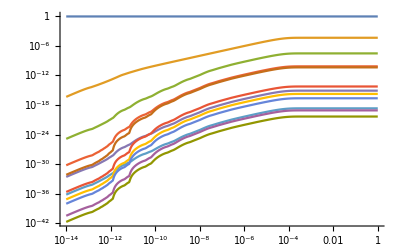

```mathematica
LogLogPlot[Evaluate[{n1[t]/n1[t],n3[t]/n1[t],n4[t]/n1[t],n5[t]/n1[t],n6[t]/n1[t],n7[t]/n1[t],n8[t]/n1[t],n9[t]/n1[t],n11[t]/n1[t],n12[t]/n1[t],n14[t]/n1[t],n15[t]/n1[t]}/. sol],{t,1*^-14,1},PlotRange->All]
```

```mathematica
Evaluate[64836*^-21*{n1[1]/n1[1],n3[1]/n1[1],n4[1]/n1[1],n5[1]/n1[1],n6[1]/n1[1],n7[1]/n1[1],n8[1]/n1[1],n9[1]/n1[1],n11[1]/n1[1],n12[1]/n1[1],n14[1]/n1[1],n15[1]/n1[1]}/. sol]
```

{{16209/250000000000000000000,(16209 n3[1])/(250000000000000000000 n1[1]),(16209 n4[1])/(250000000000000000000 n1[1]),(16209 n5[1])/(250000000000000000000 n1[1]),(16209 n6[1])/(250000000000000000000 n1[1]),(16209 n7[1])/(250000000000000000000 n1[1]),(16209 n8[1])/(250000000000000000000 n1[1]),(16209 n9[1])/(250000000000000000000 n1[1]),(16209 n11[1])/(250000000000000000000 n1[1]),(16209 n12[1])/(250000000000000000000 n1[1]),(16209 n14[1])/(250000000000000000000 n1[1]),(16209 n15[1])/(250000000000000000000 n1[1])}}

```mathematica
Evaluate[{n1[0.5]}/.sol]
```

{{n1[0.5]}}